# Social Architecture of Capitalism simulation

## Simulate

```mathematica
Get["sac.m",Path->NotebookDirectory[]];
```

Set number of agents, number of simulations, and number of simulation steps

```mathematica
n=300;
m=10;
t=50000;
```

Run the simulation

```mathematica
histories=Map[Simulate[n,t]&,Range[m]];
```

Drop any burn-in period

```mathematica
effectiveHistories=Map[Take[#,-(7 t)/10]&,histories];
```

## Analysis

### Unemployment

```mathematica
unemployed=Unemployed/@effectiveHistories;
```

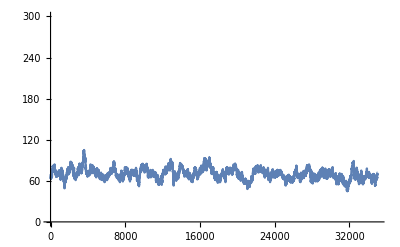
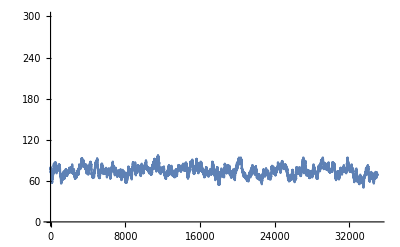
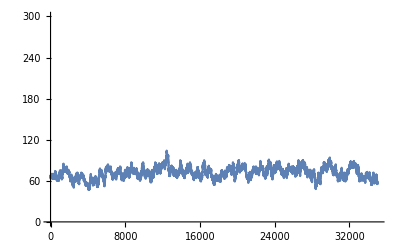
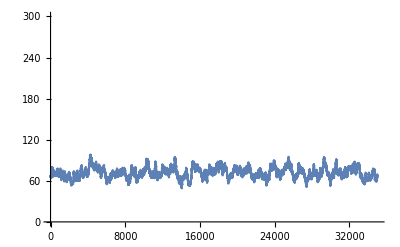
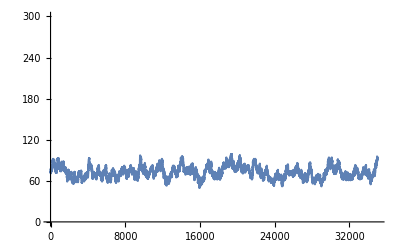
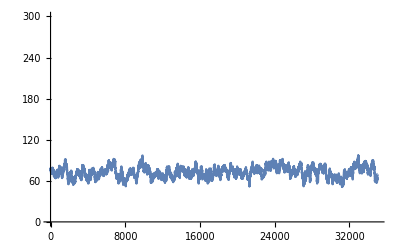
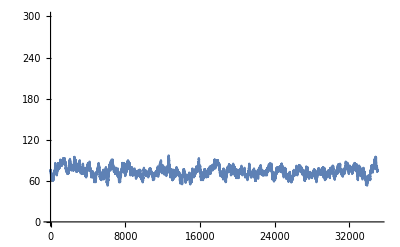
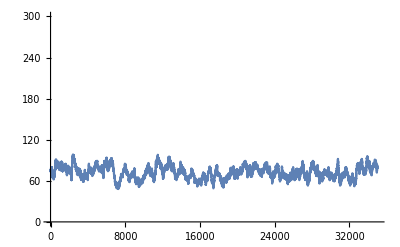

```mathematica
Map[ListPlot[#,Joined->True,PlotRange->{All,{0,n}}]&,unemployed]
```

### Firm profit rates

```mathematica
firmHistories=FirmHistories/@effectiveHistories;
```

```mathematica
firmProfitRates=FirmProfitRates/@firmHistories;
```

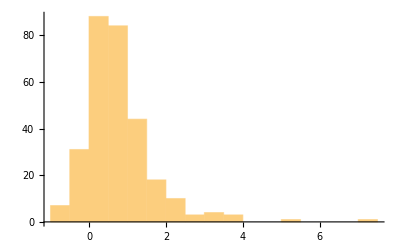
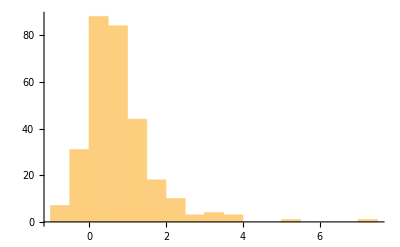
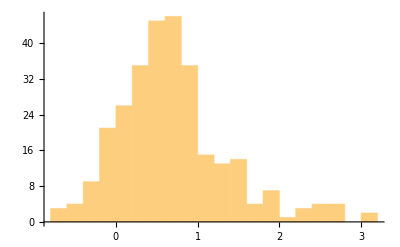
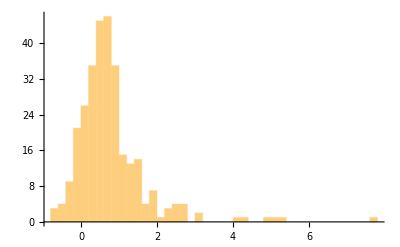
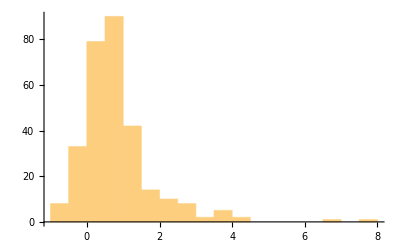
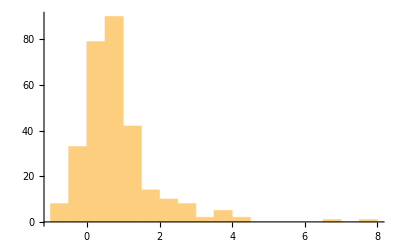
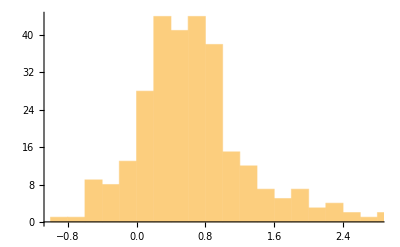
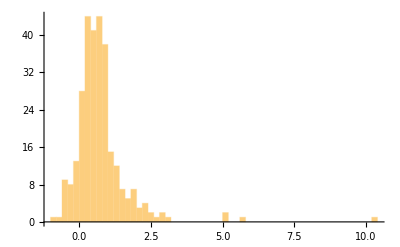

```mathematica
Map[Row[{Histogram[#],Histogram[#,PlotRange->All]}]&,firmProfitRates]
```

### Average firm size

```mathematica
averageFirmSizes=AverageFirmSizes/@ effectiveHistories;
```

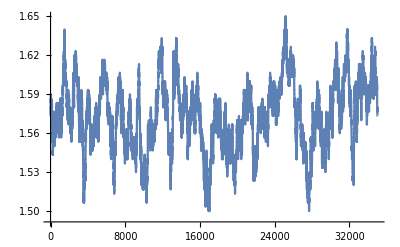
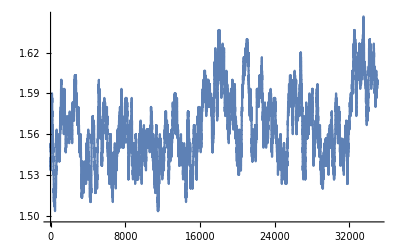
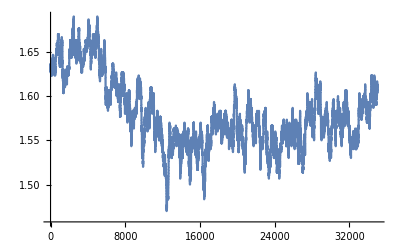
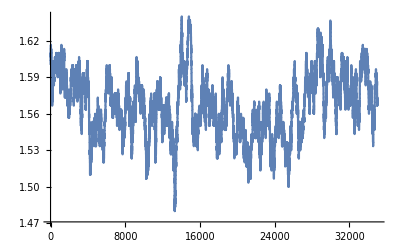
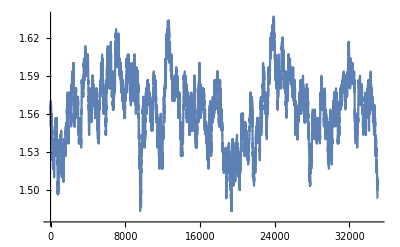
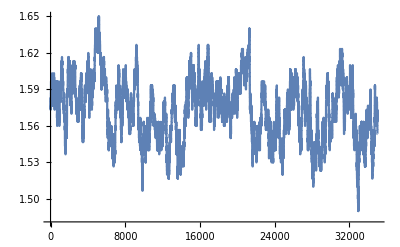
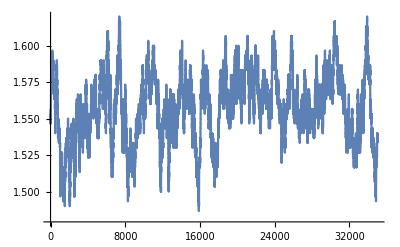
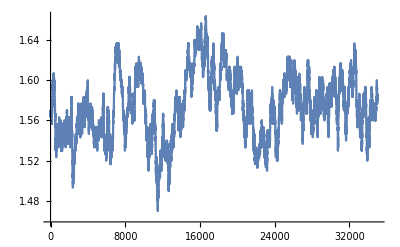

```mathematica
Map[ListPlot[#,Joined->True,PlotRange->All]&,averageFirmSizes]
```

### Firm sizes

```mathematica
firmSizes=FirmSizes/@effectiveHistories;
```

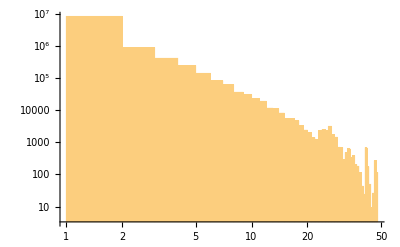
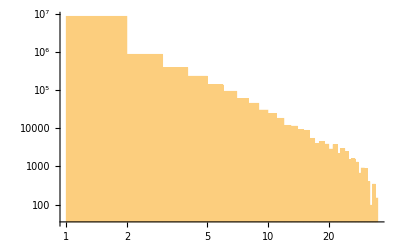
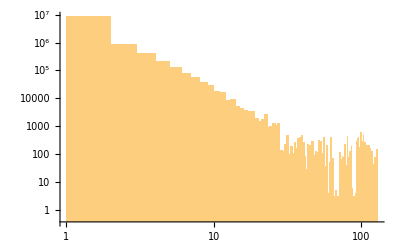
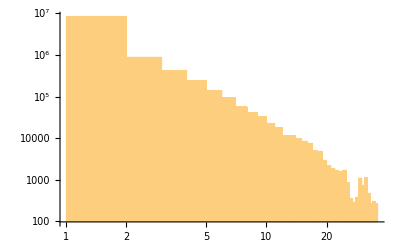
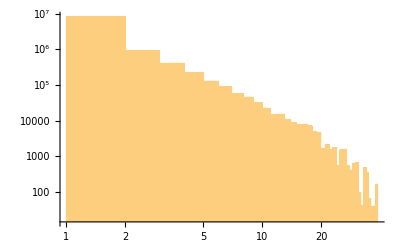
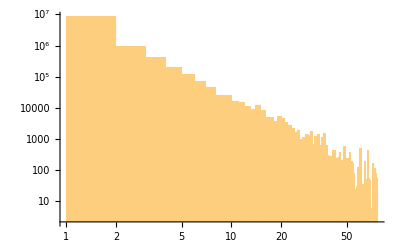
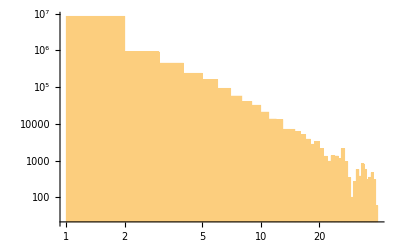
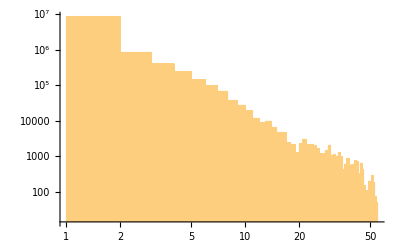

```mathematica
(* Should be a straight line *)
Map[Histogram[#,PlotRange->All,ScalingFunctions->{"Log","Log"}]&,firmSizes]
```

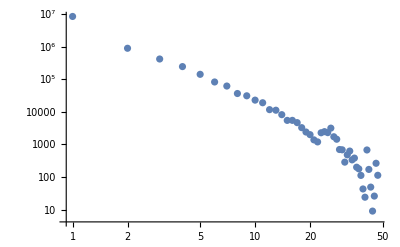
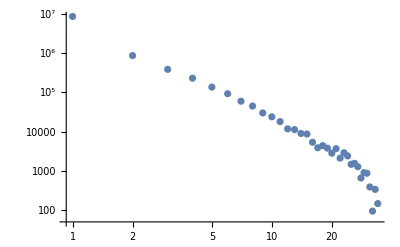
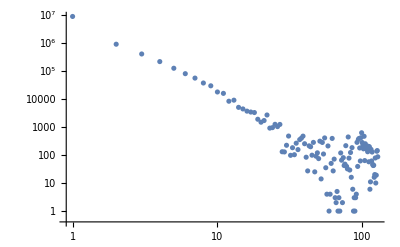
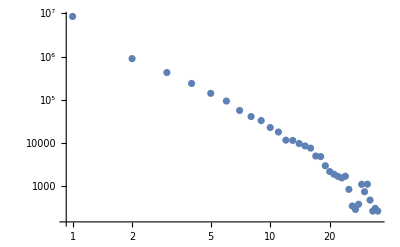
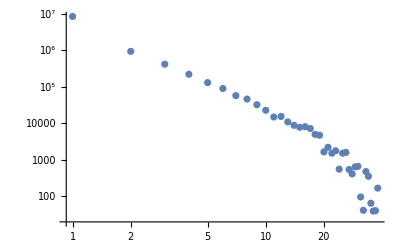
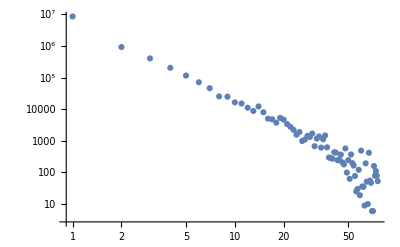
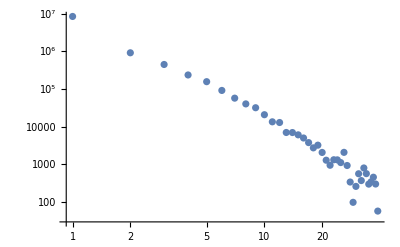
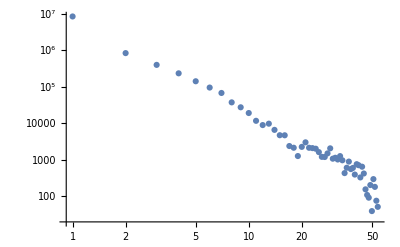

```mathematica
Map[ListPlot[Drop[BinCounts[#],1],ScalingFunctions->{"Log","Log"},PlotRange->All]&,firmSizes]
```

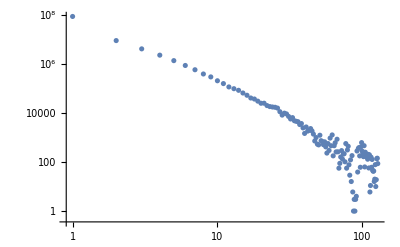

```mathematica
(* Should be a straight-line, Zipf distribution *)
ListPlot[Drop[BinCounts[Join@@firmSizes],1],ScalingFunctions->{"Log","Log"},PlotRange->All]
```

```mathematica
firmSizesSample=RandomSample[Join@@firmSizes,Round[Length[Join@@firmSizes]*0.01]];
```

```mathematica
EstimatedDistribution[firmSizesSample,ZipfDistribution[a,b]]
```

ZipfDistribution[127,1.73218]

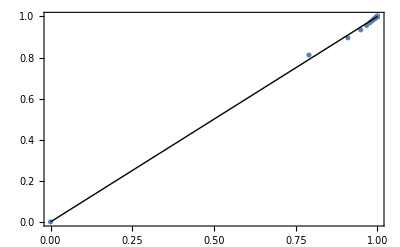

```mathematica
ProbabilityPlot[firmSizesSample,ZipfDistribution[a,b],PlotRange->All]
```

### Workers’ money

```mathematica
workersMoney=WorkersMoney/@effectiveHistories;
```

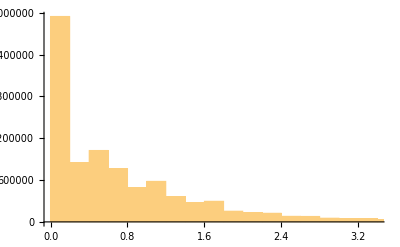
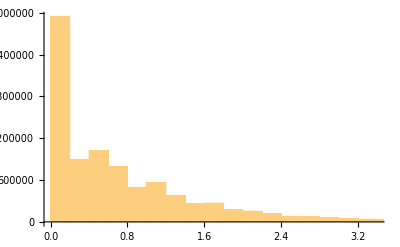
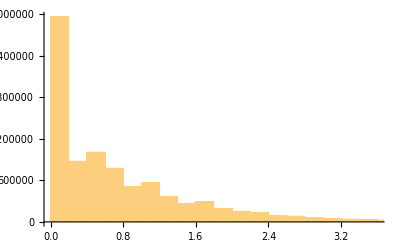
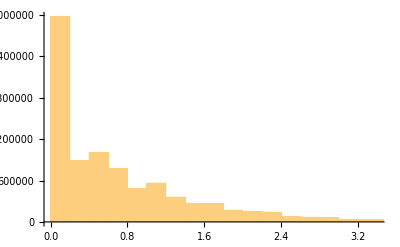
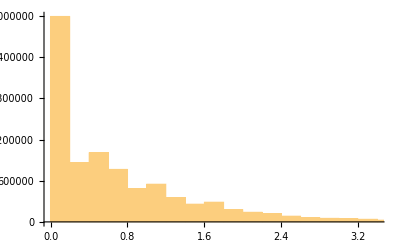
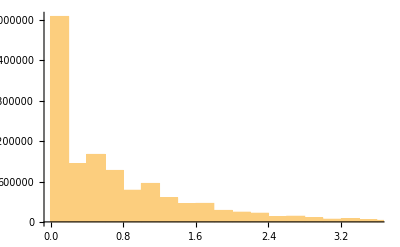
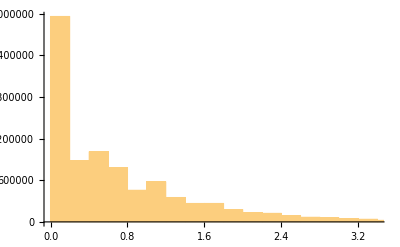
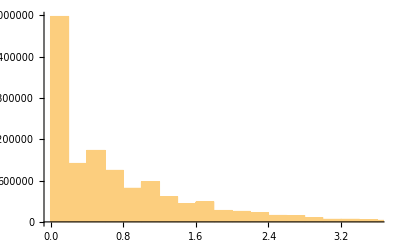

```mathematica
Histogram/@workersMoney
```

```mathematica
workersMoneySample=RandomSample[Join@@workersMoney,Round[Length[Join@@workersMoney]*0.01]];
```

```mathematica
FindDistribution[workersMoneySample,TargetFunctions->"Continuous",MaxItems->3,PerformanceGoal->"Quality"]
```

MixtureDistribution[{0.842179,0.157821},{GammaDistribution[0.449108,1.27542],LogNormalDistribution[0.219426,0.8376]}]

```mathematica
ProbabilityPlot[workersMoneySample,GammaDistribution[a,b]]
```

-Graphics-

### Workers’ wealth

```mathematica
workersWealth=EmployeesWealth/@effectiveHistories;
```

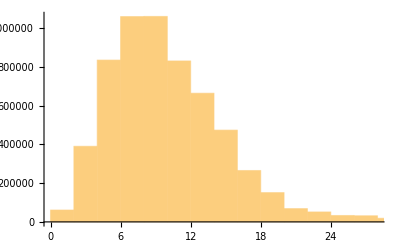
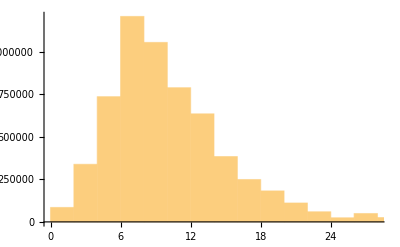
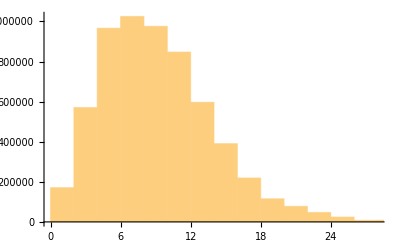
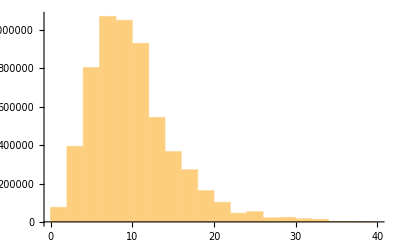
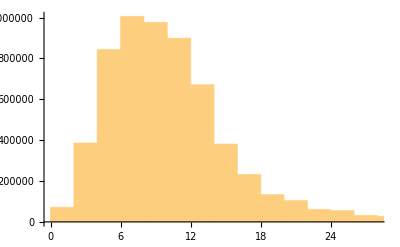
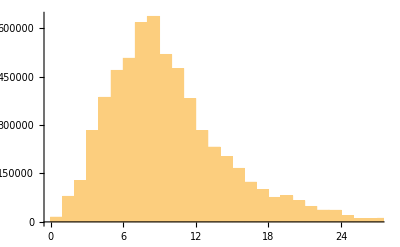
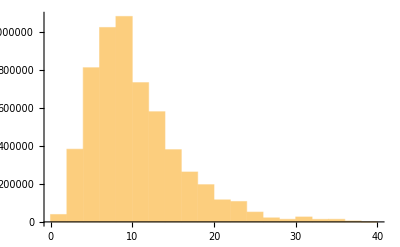
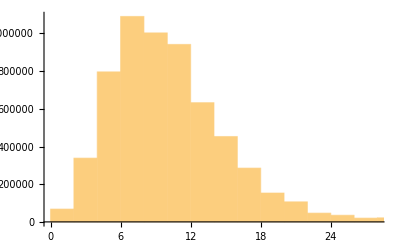

```mathematica
Histogram/@workersWealth
```

```mathematica
workersWealthSample=RandomSample[Join@@workersWealth,Round[Length[Join@@workersWealth]*0.01]];
```

```mathematica
ProbabilityPlot[workersWealthSample,GammaDistribution[a,b]]
```

-Graphics-

```mathematica
FindDistribution[workersWealthSample,TargetFunctions->"Continuous",MaxItems->3,PerformanceGoal->"Quality"]
```

ExtremeValueDistribution[7.18722,4.1033]

### Employers’ money

```mathematica
employersMoney=EmployersMoney/@effectiveHistories;
```

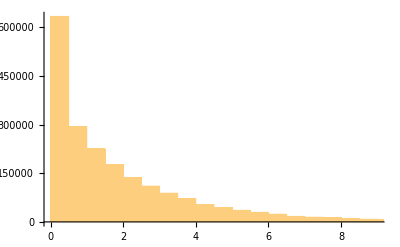
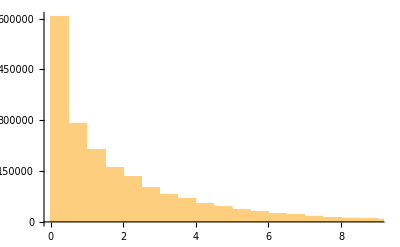
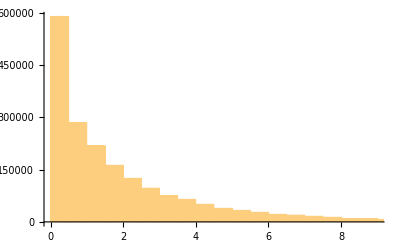
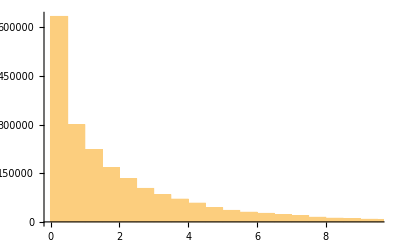
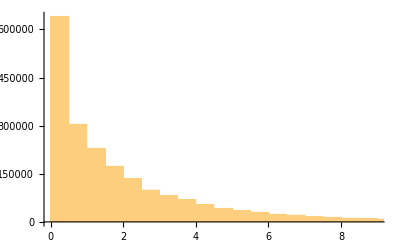
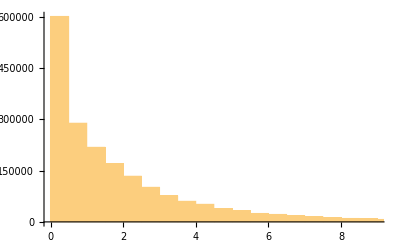
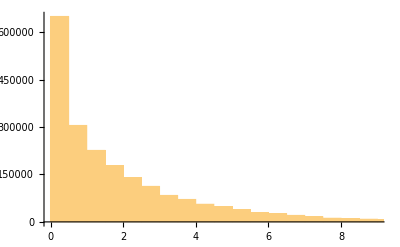
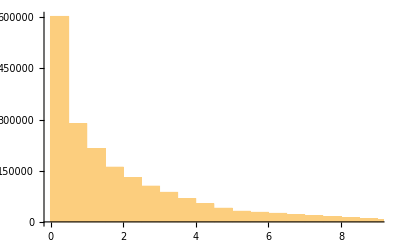

```mathematica
Histogram/@employersMoney
```

```mathematica
employersMoneySample=RandomSample[Join@@employersMoney,Round[Length[Join@@employersMoney]*0.01]];
```

```mathematica
(* N.B. c=0 means location parameter is inoperative, and so reduces to ParetoDistribution[a,b] *)
EstimatedDistribution[employersMoneySample,ParetoDistribution[a,b,d]]
```

ParetoDistribution[5.03456,3.40714,1.21117×10^-9]

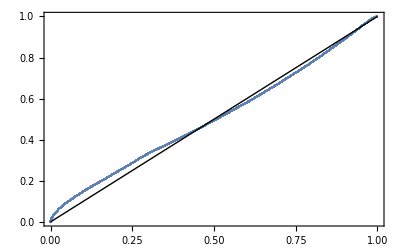

```mathematica
ProbabilityPlot[employersMoneySample,ParetoDistribution[a,b,d]]
```

```mathematica
FindDistribution[employersMoneySample,TargetFunctions->"Continuous",MaxItems->3,PerformanceGoal->"Quality"]
```

GammaDistribution[0.578227,3.42096]

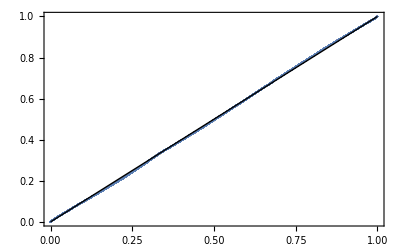

```mathematica
ProbabilityPlot[employersMoneySample,GammaDistribution[a,b]]
```

### Employers’ wealth (firm capital)

```mathematica
employersWealth=EmployersWealth/@effectiveHistories;
```

```mathematica
employersWealthSample=RandomSample[Join@@employersWealth,Round[Length[Join@@employersWealth]*0.01]];
```

```mathematica
(* N.B. c=0 means location parameter is inoperative, and so reduces to ParetoDistribution[a,b] *)
EstimatedDistribution[employersWealthSample,ParetoDistribution[a,b,d]]
```

ParetoDistribution[45886.9,3060.82,0.386211]

```mathematica
ProbabilityPlot[employersWealthSample,ParetoDistribution[a,b,d]]
```

-Graphics-

```mathematica
FindDistribution[employersWealthSample,TargetFunctions->"Continuous",MaxItems->3,PerformanceGoal->"Quality"]
```

FrechetDistribution[6.09284,35.2951,-24.2122]

```mathematica
ProbabilityPlot[employersWealthSample,FrechetDistribution[a,b,d]]
```

-Graphics-